# Lagrangian Dynamics

This is a a point mass moving in parabolic bowl with no friction. The height of the bowl is z=alpha*r^2 where r is the cylindrical r, the distance from the z axis.

-Graphics-

```mathematica
Quit[]
```

This problem shows a technique of expressing Cartesian coordinates in terms of more natural coordinates. It has the advantage of being pretty simple to implement, but the disadvantage that you can copy and paste without turning on your brain. It’s usually better to think through the problems more from the beginning, but if you get bogged down finding valid expressions for T and U, this approach can help.

Fix a Cartesian coordinate axis (one for each object in general). Be sure the origin doesn’t move!
Decide what the natural coordinates are and write x, y, and z in terms of those. Be sure you write the coordinates as functions of time.
Include any equations of constraint (equations that relate one variable to others, such as the equation for z here).
Take the derivatives.

```mathematica
x[t]=r[t]* Cos [phi[t]];
xdot=D[x[t],t]
y[t]=r[t]*  Sin[phi[t]];
ydot=D[y[t],t]
z[t]=alpha*r[t]^2;
zdot=D[z[t],t]
```

-r[t] Sin[phi[t]] phi'[t]+Cos[phi[t]] r'[t]

Cos[phi[t]] r[t] phi'[t]+Sin[phi[t]] r'[t]

2 alpha r[t] r'[t]

The kinetic energy will be 1/2 m x’[t]^2+1/2 m y’[t]^2+1/2 m z’[t]^2 in general. You really don’t have to think through things much as long as your equations for x, y, and z are OK. 

But before we write the Lagrangian, we need to write r, rdot, theta, and thetadot as if they are all independent variables. So we can do a generic substitution here.

```mathematica
xdot=xdot/.{phi[t]->phi,phi'[t]->phidot,r[t]->r,r'[t]->rdot}
ydot=ydot/.{phi[t]->phi,phi'[t]->phidot,r[t]->r,r'[t]->rdot}
zdot=zdot/.{phi[t]->phi,phi'[t]->phidot,r[t]->r,r'[t]->rdot}
```

rdot Cos[phi]-phidot r Sin[phi]

phidot r Cos[phi]+rdot Sin[phi]

2 alpha r rdot

... And we need to do the same for x, y, and z.

```mathematica
x=x[t]/.{phi[t]->phi,r[t]->r}
y=y[t]/.{phi[t]->phi,r[t]->r}
z=z[t]/.{phi[t]->phi,r[t]->r}
```

r Cos[phi]

r Sin[phi]

alpha r^2

Now the Lagrangian is very easy.

```mathematica
T=1/2 m xdot^2 +1/2 m ydot^2+1/2m zdot^2
U=m g z
L=T-U//Simplify
```

2 alpha^2 m r^2 rdot^2+1/2 m (rdot Cos[phi]-phidot r Sin[phi])^2+1/2 m (phidot r Cos[phi]+rdot Sin[phi])^2

alpha g m r^2

1/2 m (-2 alpha g r^2+phidot^2 r^2+rdot^2+4 alpha^2 r^2 rdot^2)

Take derivatives with respect to everything and put in explicit time dependence while we're at it.

```mathematica
pr=D[L,rdot]/.{r->r[t],phi->phi[t],rdot->r'[t],phidot->phi'[t]}
pphi=D[L,phidot]/.{r->r[t],phi->phi[t],rdot->r'[t],phidot->phi'[t]}
dr=D[L,r]/.{r->r[t],phi->phi[t],rdot->r'[t],phidot->phi'[t]}
dphi=D[L,phi]/.{r->r[t],phi->phi[t],rdot->r'[t],phidot->phi'[t]}
```

1/2 m (2 r'[t]+8 alpha^2 r[t]^2 r'[t])

m r[t]^2 phi'[t]

1/2 m (-4 alpha g r[t]+2 r[t] phi'[t]^2+8 alpha^2 r[t] r'[t]^2)

0

Now create the differential equations.

```mathematica
req=D[pr,t]==dr//Simplify
phieq=D[pphi,t]==dphi//Simplify
```

m (r[t] (-phi'[t]^2+2 alpha (g+2 alpha r'[t]^2))+r''[t]+4 alpha^2 r[t]^2 r''[t])==0

m r[t] (2 phi'[t] r'[t]+r[t] phi''[t])==0

Define the variables, add initial conditions, and solve the equations.

```mathematica
m=0.1;
alpha=0.1;
g=9.8;
sol1=NDSolve[{req,phieq,r[0]==.05,phi[0]==0,r'[0]==0.1,phi'[0]==3},{r[t],phi[t]},{t,0,10}]
```

{{r[t]→InterpolatingFunction[…][t],phi[t]→InterpolatingFunction[…][t]}}

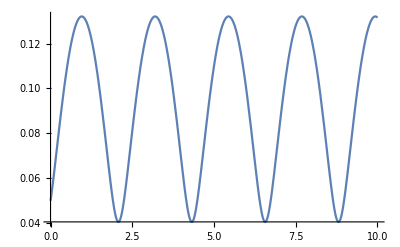

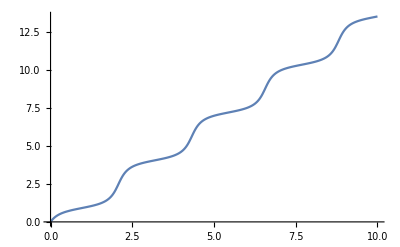

```mathematica
r[t_]=r[t]/.sol1[[1]];
phi[t_]=phi[t]/.sol1[[1]];
Plot[r[t],{t,0,10}]
Plot[phi[t],{t,0,10}]
```

```mathematica
ParametricPlot[{r[t]*Cos[phi[t]],r[t]*Sin[phi[t]]},{t,0,10}]
```